```mathematica
7200*Sum[Binomial[23,i],{i,0,3}]
```

14745600

```mathematica
2^23
```

8388608

```mathematica
Join[Quantity[#,"Fahrenheit"]&/@Range[0,100,5],Quantity[#,"Celsius"]&/@Range[-15,35,5]]
SortBy[%,UnitConvert]
```

{0 °F,5 °F,10 °F,15 °F,20 °F,25 °F,30 °F,35 °F,40 °F,45 °F,50 °F,55 °F,60 °F,65 °F,70 °F,75 °F,80 °F,85 °F,90 °F,95 °F,100 °F,-15 °C,-10 °C,-5 °C,0 °C,5 °C,10 °C,15 °C,20 °C,25 °C,30 °C,35 °C}

{0 °F,-15 °C,5 °F,10 °F,-10 °C,15 °F,20 °F,-5 °C,25 °F,30 °F,0 °C,35 °F,40 °F,5 °C,45 °F,10 °C,50 °F,55 °F,15 °C,60 °F,65 °F,20 °C,70 °F,75 °F,25 °C,80 °F,85 °F,30 °C,90 °F,35 °C,95 °F,100 °F}

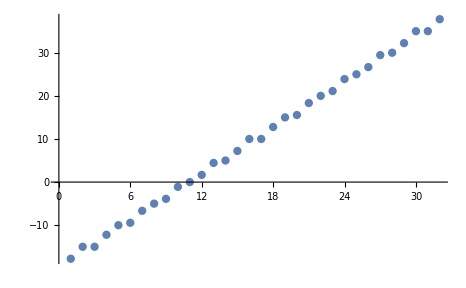

```mathematica
ListPlot[UnitConvert[#,"Celsius"]&/@%293]
```

```mathematica
?UnitConvert
```

UnitConvert[quantity,targetunit] attempts to convert the specified quantity to the specified targetunit.
UnitConvert[quantity] converts the specified quantity to SI base units.

```mathematica
UnitConvert[Quantity[-17.5,"Fahrenheit"],"Celsius"]
```

-27.5 °C

```mathematica
?Double
```

Missing[UnknownSymbol,Double]